```mathematica
Clear["Global`*"]
```

```mathematica
Ro[A_,W_]=√((Lm*Lh*bh*(ⅇ^-(A))*bm*(ⅇ^-(A))*alph*alpm*(1-(12.58/(K*(ⅇ^-(W+A))))))/(mum*(ⅇ^(W))*muh*((mum*(ⅇ^(W)))+phim)*(muh+phih+gh)*(alph+muh)*(alpm+(mum*(ⅇ^(W))))))

R0sym=Ro[A,W];
```

√((alph alpm bh bm ⅇ^(-2 A-W) (1-(12.58 ⅇ^(A+W))/K) Lh Lm)/(muh (alph+muh) mum (alpm+ⅇ^W mum) (gh+muh+phih) (ⅇ^W mum+phim)))

```mathematica
paramValues={Lh->0.000046,bh->0.75,alph->0.1667,gh->0.328833,muh->0.000046,phih->0.0005,Lm->0.025,bm->0.375,alpm->0.1428,mum->0.025,phim->0.00530856625,K->100};
```

```mathematica
scenarioRules=Join[paramValues,{A->0.9,W->0.9}];   (*30 % coverage*)
R0val=N[R0sym/. scenarioRules];
Print["R₀(A=0.3, W=0.3) = ",R0val];
```

R₀(A=0.3, W=0.3) = 0.378752

```mathematica
params={Lh,bh,alph,gh,muh,phih,Lm,bm,alpm,mum,phim,A,W};   (*K removed*)
names={"λh","βh","αh","γ","μh","φh","λm","βm","αm","μm","φm","A","W"};                     

elasticities=Table[With[{s=params[[i]],nm=names[[i]]},(*s is now the SYMBOL*){nm,N[(s/R0sym)*D[R0sym,s]/. scenarioRules]} (*differentiate w.r.t.s*)],{i,Length[params]}];

TableForm[elasticities,TableHeadings->{None,{"Parameter","Elasticity"}}]
```

Parameter | Elasticity
λh | 0.5
βh | 0.5
αh | 0.000137934
γ | -0.499171
μh | -0.500208
φh | -0.000759004
λm | 0.5
βm | 0.5
αm | 0.150497
μm | -1.11076
φm | -0.0397356
A | -2.3332
W | -2.43289

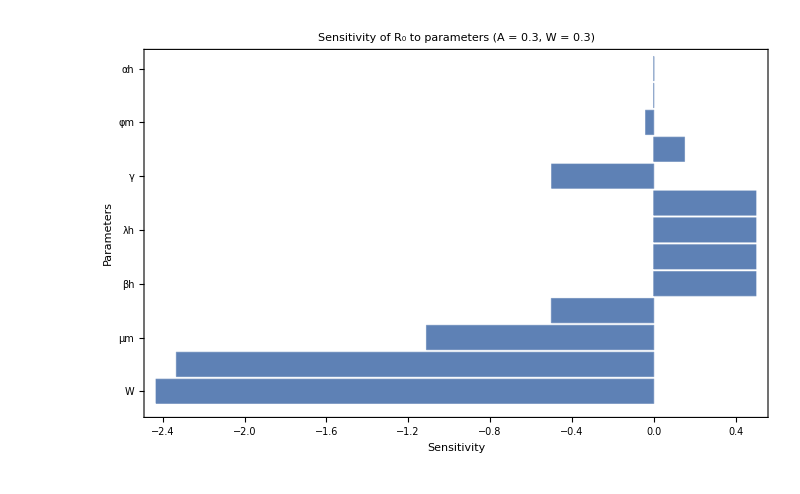

```mathematica
(*sort by|elasticity|,largest first*)sorted=SortBy[elasticities,-Abs[#[[2]]]&];

BarChart[sorted[[All,2]],ChartLabels->sorted[[All,1]],PlotLabel->Style["Sensitivity of R₀ to parameters\n(A = 0.3, W = 0.3)",Bold,14],FrameLabel->{Style["Parameters",12,Bold],Style["Sensitivity",12,Bold]},Frame->True,GridLines->{None,{0}},ImageSize->{800,400},PlotRange->All,ChartStyle->ColorData[97,1],BarOrigin->Left]
```

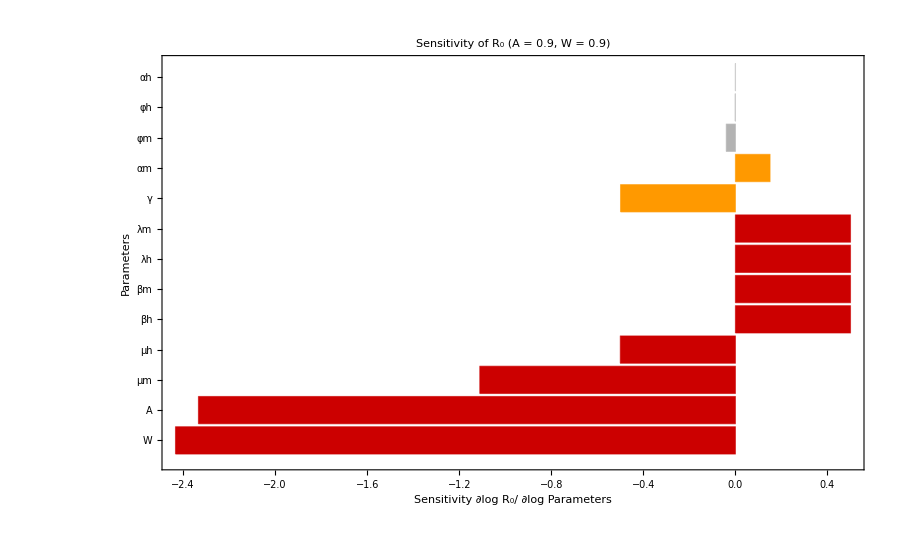

```mathematica
(*1.  sort by absolute size,largest first*)sorted=SortBy[elasticities,-Abs[#[[2]]]&];

(*2.  colour function*)
colours=Table[Which[Abs[bar]<0.1,GrayLevel[0.7],(*low*)Abs[bar]<0.5,RGBColor[1,0.6,0],(*mild*)True,RGBColor[0.8,0,0]       (*high*)],{bar,sorted[[All,2]]}];


BarChart[sorted[[All,2]],ChartLabels->sorted[[All,1]],PlotLabel->Style[Row[{"Sensitivity of R₀ (A = 0.9, W = 0.9)"}],Bold,14],FrameLabel->{Style["Parameters",12,Bold],Style["Sensitivity  ∂log R₀/ ∂log Parameters",12,Bold]},Frame->True,GridLines->{None,{0}},ImageSize->{900,450},PlotRange->All,ChartStyle->colours,BarOrigin->Left]
```

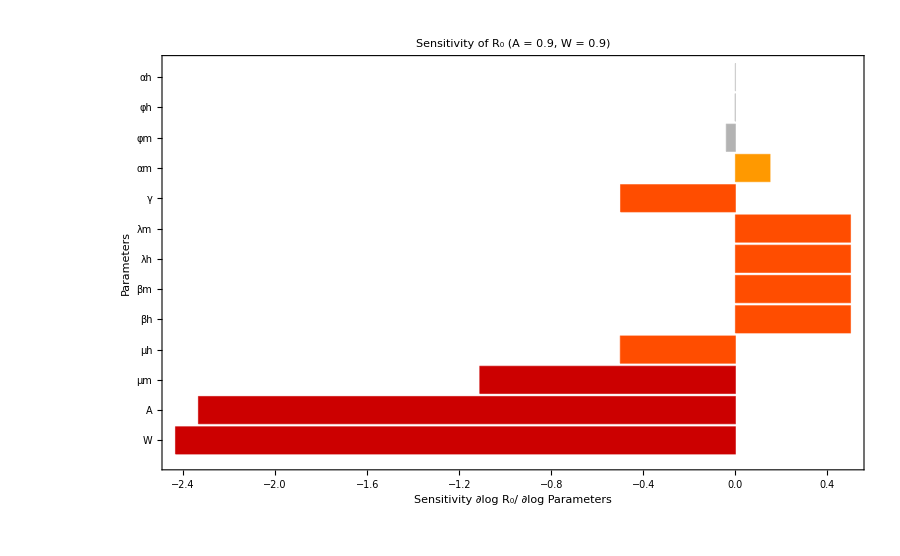

```mathematica
sorted=SortBy[elasticities,-Abs[#[[2]]]&];

(*----------2.  continuous colour function----------*)colours=Table[Which[Abs[bar]<0.1,GrayLevel[0.7],(*low impact*)Abs[bar]<0.3,RGBColor[1,0.6,0],(*mild impact*)0.3<=Abs[bar]<0.6,RGBColor[1,0.3,0],(*medium impact*)Abs[bar]>=0.6,RGBColor[0.8,0,0]        (*high impact*)],{bar,sorted[[All,2]]}];


BarChart[sorted[[All,2]],ChartLabels->sorted[[All,1]],PlotLabel->Style[Row[{"Sensitivity of R₀ (A = 0.9, W = 0.9)"}],Bold,14],FrameLabel->{Style["Parameters",12,Bold],Style["Sensitivity  ∂log R₀/ ∂log Parameters",12,Bold]},Frame->True,GridLines->{None,{0}},ImageSize->{900,450},PlotRange->All,ChartStyle->colours,BarOrigin->Left]
```